## Global Properties

### Packages

```mathematica
Needs["NumericalCalculus`"]
Needs["DifferentialEquations`NDSolveProblems`"];
Needs["DifferentialEquations`NDSolveUtilities`"];
<<MaTeX`
SetOptions[MaTeX,"Preamble"->{"\\usepackage{xcolor, color,txfonts}"}];
```

### Setup

```mathematica
SetOptions[MaTeX,"Preamble"->{"\\usepackage{xcolor, color, txfonts, amsfonts, amssymb, ulem, amsmath}"},Magnification->1.3];
colors=ColorData[10,"ColorList"];
colorsb=Reverse[ColorData[10, "ColorList"]];
tex:=MaTeX;
SetOptions[{Plot,LogPlot,ListLinePlot, ListLogPlot,LogLogPlot,ListPlot,ListLogLinearPlot,ListLogLogPlot,LogLinearPlot,ParametricPlot},
Frame->True, FrameStyle->Black, PlotStyle-> Join[{Black, Blue}, colors, {colors[[1]]}],  ImageSize->350, Background->White, PlotRangePadding->None];
SetDirectory[NotebookDirectory[]];
```

### SM Inputs (DO WE NEED THESE? ARE THEY MODIFIED?)

```mathematica
vh=246;  (*GeV*)

mh=125+18/100; (*GeV *);
mW=80.385; (* GeV*)
mZ= 91.1875; (* GeV*)
mt= 173.1; (* GeV *)

(*λh=(125/246)^2;*)
λh=(mh/vh)^2;

alpha1Z=.016830; 
alpha2Z=.03347;
alpha3Z=.1184;
(*
g2Z=Sqrt[4Pi alpha2Z];
gpZ = Sqrt[3/5]g1Z;
*)
g2Z=Sqrt[mW^2/vh^2*4];
gpZ=Sqrt[mZ^2*4 /vh^2-g2Z^2];



yt=Sqrt[2]*mt/vh;

fourπvh=4Pi vh;
```

### Particle Data

```mathematica
mu= .0022; (* GeV *)
md= .0046; (* GeV *)
mcharm= 1.28; (* GeV *)
mstrange= .096; (* GeV *)
mt= 173.1; (* GeV *)
mb= 4.18; (* GeV *)

melec= .000511; (* GeV *)
mμ= .1057; (* GeV *)
mτ= 1.77686; (* GeV *)
mνe= 0; (* GeV *)
mνμ= 0; (* GeV *)
mντ= 0; (* GeV *)

mh=125.18; (*GeV*)
mH=mh; (* for compatibility with Gilly's xsec code *)
mW=80.385; (* GeV*)
mZ= 91.1875; (* GeV*)
mπ0=.135; (* GeV*)
mπpm=.1396; (* GeV*)


Mpl= 2.4*10^18; (*GeV *)
Λqcd=.2;  (*GeV*)
```

Particle data in format :
   name -> { mass, 
  	hypercharge, 
  	N_c, spin/polarization dof, 
  	dof that go into calculating gSeff, 
  	{range of energies that dof are active}}

```mathematica
SM={

uL->{mu, 1/6,  3, 2,2,{Λqcd, Mpl}}, 
uR->{mu, -2/3 ,  3, 2,2,{ Λqcd, Mpl}},
dL->{md, 1/6,  3, 2,2, {Λqcd, Mpl}},
dR->{md, 1/3,  3, 2,2,{Λqcd, Mpl}},
cL->{mcharm,  1/6 , 3,2,2,{mcharm, Mpl}},
cR->{mcharm,  -2/3 , 3,2,2,{mcharm, Mpl}},
sL->{mstrange,1/6,   3,2,2,{Λqcd, Mpl}},
sR->{mstrange, 1/3,  3, 2,2,{Λqcd, Mpl}},
bL->{mb,1/6,  3, 2,2, {mb, Mpl}},
bR->{mb,  1/3,  3, 2,2, {mb, Mpl}},
tL->{mt,  1/6,  3, 2,2, {mt, Mpl}},
tR->{mt,  -2/3 , 3, 2,2, {mt, Mpl}},
eL->{melec, -1/2,  1, 2,2, {melec, Mpl}},
eR->{melec, 1,  1, 2,2, {melec, Mpl}},
μL->{mμ,-1/2,  1, 2,2, {mμ, Mpl}},
μR->{mμ, 1,   1, 2,2, {mμ, Mpl}},
τL->{mτ,-1/2,  1, 2,2, {mτ, Mpl}},
τR->{mτ, 1,  1, 2,2, {mτ, Mpl}},
νe->{mνe,0,   1,2+2.137*8/7,2+1.591*8/7, {800*10^-6, Mpl}},(* the g, gS dof indices come from 1609.04979 Table 2 and a bit of algebra to reproduce the right result *)
νμ->{mνμ, 0, 1,2-2.137/2*8/7,2-1.591/2*8/7, {0, Mpl}}, (* the g, gS dof indices come from 1609.04979 Table 2 and a bit of algebra to reproduce the right result   *)
ντ->{mντ, 0, 1,2-2.137/2*8/7,2-1.591/2*8/7, {0, Mpl}},(* the g, gS dof indices come from 1609.04979 Table 2 and a bit of algebra to reproduce the right result  *)



G->{0,0,   8, 2,2, {Λqcd, Mpl}},
photon->{0,0, 1, 2,2,{0, Mpl}},
h->{mh,0, 1, 1, 1,{mh, Mpl}},
Wp->{mW,1, 1,  3,3,{mW, Mpl}},
Wm->{mW,-1,1,  3,3,{mW, Mpl}},
Z->{mZ,0, 1,  3,3,{mZ, Mpl}},

π0->{mπ0, 0,1, 1,1,{mπ0, Λqcd}}, 
πp->{mπpm, 1, 1, 1,1,{mπpm, Λqcd}}, 
πm->{mπpm, -1, 1, 1,1,{mπpm, Λqcd}}, 

fermions->{uL, uR,  dL,dR,  cL,cR,  sL, sR, bL, bR, tL, tR, eL, eR, μL, μR, τL, τR, νe, νμ, ντ}, 

fermionMassEigens->{uL,   dL,  cL, sL, bL, tL,  eL, μL, τL}, 
quarks->{uL, uR,  dL,dR,  cL,cR,  sL, sR, bL, bR, tL, tR},
quarkMassEigens->{uL,   dL,  cL, sL, bL, tL},

bosons->{ G, Wp, Wm, Z, photon, h, π0, πp, πm}

};
massIndex=1;
QemIndex=2;
HyperchargeIndex=2;
NcIndex=3;
spinIndex=4; (* or polarization index. Also the index that parameterizes number of degrees of degrees of freedom that freeze out at a certain temperature, in the case of neutrinos*)
gSindex=5; (* The index that parameterizes number of degrees of degrees of freedom that go into calculating gS,  that freeze out at a certain temperature, in the case of neutrinos*)
freezeoutIndex=6;
```

### Hubble and active DOF

```mathematica
σvWIMP = (3×10^-26)/(2 10^10(2 10^-14)^2) ;
rlcAbndnce= 4 *10^(-10);(* GeV *)
snow=2970 /cm3TOGeV3;
Tnow=2.73 *GeVperK;
TmatterRadEq=2*10^-9;(* GeV *)
```

First we write out the effective degrees of freedom as step functions, but eventually we will interpolate as we 
want smooth invertible functions.

```mathematica
HeavisideInvertible[x_]:=Module[
{a=10^-5}, 
1/Pi(ArcTan[1/a*x]+Pi/2)
];
geff[T_, model_]:=Module[{
i, gactive=0, fermion, boson
}, 

For[i=1, i≤Length[fermions/.model ], i++, 
fermion=(fermions/.model)[[i]]/.model;
gactive=gactive+7/8fermion[[NcIndex]]*fermion[[spinIndex ]]*(HeavisideInvertible[T-fermion[[freezeoutIndex]][[1]]]-HeavisideInvertible[T-fermion[[freezeoutIndex]][[2]]])
];

For[i=1, i≤Length[bosons/.model], i++, 
boson=(bosons/.model)[[i]]/.model;
gactive=gactive+boson[[NcIndex]]*boson[[spinIndex ]]*((HeavisideInvertible[T-boson[[freezeoutIndex]][[1]]]-HeavisideInvertible[T-boson[[freezeoutIndex]][[2]]]))];
gactive
];

gSeff[T_, model_]:=Module[{
i, gactive=0, fermion, boson
}, 

For[i=1, i≤Length[fermions/.model ], i++, 
fermion=(fermions/.model)[[i]]/.model;
gactive=gactive+7/8fermion[[NcIndex]]*fermion[[gSindex]](HeavisideInvertible[T-fermion[[freezeoutIndex]][[1]]]-HeavisideInvertible[T-fermion[[freezeoutIndex]][[2]]])
];

For[i=1, i≤Length[bosons/.model], i++, 
boson=(bosons/.model)[[i]]/.model; 
gactive=gactive+boson[[NcIndex]]*boson[[gSindex]]((HeavisideInvertible[T-boson[[freezeoutIndex]][[1]]]-HeavisideInvertible[T-boson[[freezeoutIndex]][[2]]]))];
gactive
];
```

The following plot can be compared against Figure 2 of 1705.01987.pdf

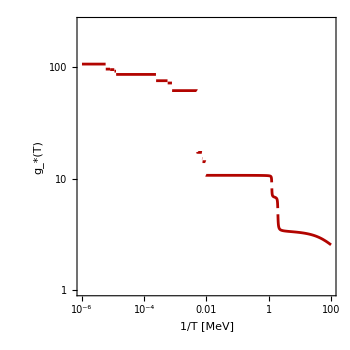

```mathematica
LogLogPlot[geff[1/(T*10^3), SM],{T,10^-6, 100}, PlotRange->{1, 250},
 Frame->True, 
Background->White,
AspectRatio->1, FrameLabel->{
Style["1/T [MeV]", Black, FontSize->14] ,
Style["g_*(T)", Black, FontSize->14]},
 FrameStyle->Thick]
```

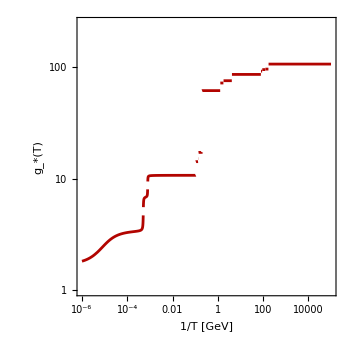

```mathematica
LogLogPlot[geff[(T), SM],{T,10^-6, 100000}, PlotRange->{1, 250},
 Frame->True, 
Background->White,
AspectRatio->1, FrameLabel->{
Style["1/T [GeV]", Black, FontSize->14] ,
Style["g_*(T)", Black, FontSize->14]},
 FrameStyle->Thick]
```

```mathematica
geff[140, SM]
```

96.25

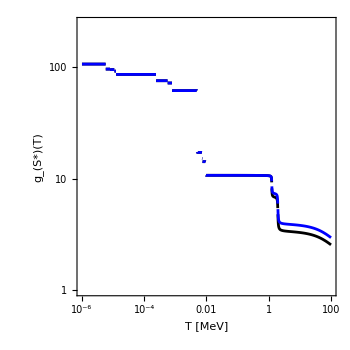

```mathematica
LogLogPlot[{geff[1/(T*10^3), SM],gSeff[1/(T*10^3), SM]},{T,10^-6, 100}, PlotRange->{1, 250},  
 Frame->True,  AspectRatio->1, FrameLabel->{Style["T [MeV]", Black, FontSize->14] ,Style["g_(S*)(T)", Black, FontSize->14]}, FrameStyle->Thick]
```

```mathematica
H[T_] := π/(3 Mpl √10) √geff[T, SM] T^2;
s[T_] := (2 π^2)/45 gSeff[T,SM] T^3;
```

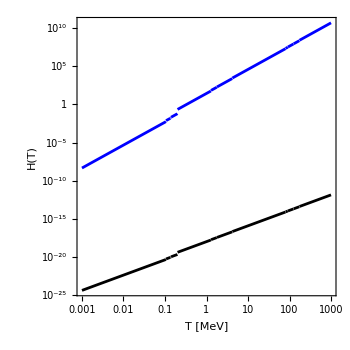

```mathematica
LogLogPlot[{H[T], s[T]}, {T, 10^-3, 10^3}, Background->White,
 Frame->True,  AspectRatio->1, FrameLabel->{Style["T [MeV]", Black, FontSize->14] ,Style["H(T)", Black, FontSize->14]}, FrameStyle->Thick]
```

## GW Power Spectrum

#### Calculate the GW power spectrum (PTplot)

```mathematica
Ssw[f_,betaH_, Tstar_, vw_]:=Module[{
fpeak,
zp=10
}, 

fpeak=8.876*10^-6  1/vw (betaH) (zp/10)(Tstar/100 (* GeV *))(geff[Tstar, SM]/100)^(1/6) (* Hz *);
(f/fpeak)^3 (7/(4+3(f/fpeak)^2))^(7/2)

];

kappaf[alpha_, vw_]:=Module[{
kappaA, 
kappaB, 
kappaC, 
kappaD, 
cs = Sqrt[1/3], 
ξJ ,
δk
},

kappaA= vw^(6/5) 6.9 alpha/(1.36 - 0.037 Sqrt[alpha]+alpha);
kappaB = alpha^(2/5) /(0.017 + (0.997+alpha)^(2/5));
kappaC= Sqrt[alpha]/(1.35 + Sqrt[ 0.98 + alpha]);
kappaD = alpha/(.73 + 0.083 Sqrt[alpha] +alpha);
δk = -.9Log[ Sqrt[alpha]/(1 + Sqrt[alpha])];

ξJ=(Sqrt[ 2/3 alpha + alpha^2] + Sqrt[1/3])/(1 + alpha);

If[ vw<cs,
cs ^(11/5) kappaA kappaB/((cs^(11/5 )- vw^(11/5))kappaB + vw cs^(6/5) kappaA), 
If[vw > ξJ, 
(ξJ -1)^3 ξJ^(5/2)vw^(-5/2) kappaC kappaD/( ( ( ξJ-1)^3- ( vw -1)^3) ξJ^(5/2) kappaC + (vw-1)^3 kappaD), 
kappaB + (vw - cs)δk + (vw-cs)^3/(ξJ - cs)^3 (kappaC-kappaB- ( ξJ - cs) δk)]]

];

OmegaSW[f_, alpha_, betaH_, Tstar_, vw_]:=Module[{
Gamma=4/3, 
vflsq, 
hplanck=.678
},


vflsq=3/4 kappaf[alpha, vw] alpha/(1+alpha);

(* 8.5*10^-6 (100/geff[Tstar, SM])^(1/3) Gamma^2 vflsq^2 (1/betaH) vw Ssw[f, betaH, Tstar, vw]*)
hplanck^2 3*.687*3.57*10^-5*.012*(8Pi)^(1/3)(100/geff[Tstar, SM])^(1/3) Gamma^2 vflsq^2 (1/betaH) vw Ssw[f, betaH, Tstar, vw]
];




Scol[f_,betaH_, Tstar_, vw_]:=Module[{
fpeak,
fstarβ,
cl=.064, 
ch=.48
}, 

fstarβ=.35/(1+0.069vw + 0.69 vw^4);
fpeak=16.5*10^-6 (fstarβ)(betaH)(geff[Tstar, SM]/100)^(1/6);
(cl ( f/fpeak)^(-3) + (1 - cl-ch)( f/fpeak)^(-1) + ch ( f/fpeak))^(-2)

];


OmegaCol[f_, alpha_, betaH_, Tstar_, vw_]:=Module[{
Delta, 
kappaphi
},

kappaphi = 0;

Delta=.48vw^3/(1+5.3vw^2 + 5vw^4);
1.67*10^-5 Delta (1/betaH)^2 (kappaphi alpha/(1+alpha))^2 (100/ geff[Tstar, SM])^(1/3) Scol[f]
];

Sturb[f_, alpha_, betaH_, Tstar_, vw_]:=Module[{
fpeak, 
hstar
},

hstar=16.5*10^-6 (* Hz *) (Tstar /100 (*GeV*)) (geff[Tstar, SM]/100)^(1/6);
fpeak = 27*10^-6 (*Hz*) /vw betaH (Tstar/100 (*GeV*)) (geff[Tstar, SM]/100)^(1/6);
(f/fpeak)^3 /((1+f/fpeak)^(11/3)(1+8Pi f/hstar))

];


OmegaTurb[f_, alpha_, betaH_, Tstar_, vw_]:=Module[{
kappaTurb (*= 1.97/65.0  (* WHY *) *)
},

kappaTurb=0.05kappaf[alpha, vw];

3.35*10^-4 1/betaH (kappaTurb alpha/(1+alpha))^(3/2) (100/geff[Tstar, SM])^(1/3)vw Sturb[f, alpha, betaH, Tstar, vw]
];


Omega[f_, alpha_, betaH_, Tstar_, vw_]:= Module[
{
vflsq, hrstar, Htsh
}, 

vflsq=3/4 kappaf[alpha, vw] alpha/(1+alpha);
hrstar=(8Pi)^(1/3)vw/betaH;
Htsh=hrstar/Sqrt[vflsq];

0+  Min[Htsh, 1]*OmegaSW[f, alpha, betaH, Tstar, vw]+ OmegaTurb[f, alpha, betaH, Tstar, vw]
];
```

#### Experimental sensitivity curves

```mathematica
GWbounds=Drop[Import["GWData/GWbounds.csv"], 1];
SKA=Interpolation[Map[{10^#[[1]], 10^#[[2]]}&, Select[GWbounds, !(#[[2]]=="")&]], InterpolationOrder->1];
Lisa=Interpolation[Map[{10^#[[1]], 10^#[[3]]}&, Select[GWbounds, !(#[[3]]=="")&]], InterpolationOrder->1];BBO=Interpolation[Map[{10^#[[1]], 10^#[[5]]}&, Select[GWbounds, !(#[[5]]=="")&]], InterpolationOrder->1];
ET=Interpolation[Map[{10^#[[1]], 10^#[[4]]}&, Select[GWbounds, !(#[[4]]=="")&]], InterpolationOrder->1];
```

## Plots

#### Comparison of m_σ/m_η' and GW signal

```mathematica
SetDirectory[NotebookDirectory[]];
data1p6N = Import["Test_N3F6_Normal.csv"];
data1p6N[[1]]
data1p6N//Length
data1p6N=Drop[data1p6N, 1];
data1p6GWN= Select[data1p6N, #[[5]]≠0&];
data1p6GWN= Select[data1p6GWN, #[[7]]>0&];
data1p6GWN//MatrixForm;

data1p6C = Import["Test_N3F6_Csaki.csv"];
data1p6C[[1]]
data1p6C//Length
data1p6C=Drop[data1p6C, 1];
data1p6GWC= Select[data1p6C, #[[5]]≠0&];
data1p6GWC= Select[data1p6GWC, #[[7]]>0&];
data1p6GWC//MatrixForm;
```

{m2,c,lambda_sigma,lambda_a,Tn,Alpha,Beta,MassRatio}

31

{m2,c,lambda_sigma,lambda_a,Tn,Alpha,Beta,MassRatio}

31

```mathematica
color=1;
style=1;
massratioC={ data1p6GWC[[1]][[8]]};
massratioN={ data1p6GWN[[1]][[8]]};
Table[
If[!MemberQ[massratioC, data1p6GWC[[i]][[8]]],AppendTo[massratioC, data1p6GWC[[i]][[8]]]],
{i, Length[data1p6GWC]}];
massratioN={ data1p6GWN[[1]][[8]]};
Table[
If[!MemberQ[massratioN, data1p6GWN[[i]][[8]]],AppendTo[massratioN, data1p6GWN[[i]][[8]]]],
{i, Length[data1p6GWN]}];
```

```mathematica
mrminC = Min[massratioC]
mrmaxC = Max[massratioC]

mrminN = Min[massratioN]
mrmaxN = Max[massratioN]
```

3.32897

3.55505

17.4068

19.1399

```mathematica
mrlistC = {3,3.5,4};
mrlistN = {17,18,19,20};
```

```mathematica
imaxC=Length[mrlistC]-1;
imaxN=Length[mrlistN]-1;
iset=1;
Show[
Join[

(* Expeimental bounds *)
{ListLogLogPlot[{
-1
}, PlotStyle->{Black, colors[[1]], Blue}, Joined->True, PlotRange->{{10^-8.5, 10^6},{10^-25, 10^-6.6}}, 
FrameLabel->{MaTeX["f [\\text{Hz}]", Magnification->1.3], MaTeX["\\Omega h^2 ", Magnification->1.3]}, ImageSize->600, 
PlotLabel->MaTeX["\\text{Comparison of mass ratio } m_\\sigma/m_{\\eta'}", Magnification->1.4]
], 

LogLogPlot[10^-6, {f, 10^-20, 10^20}, PlotStyle->Gray, Filling->Top, PlotRange->{10^-30, 10^30}],
LogLogPlot[SKA[f], {f,SKA[[1]][[1]][[1]],SKA[[1]][[1]][[2]]}, PlotStyle->Gray, Filling->Top],
LogLogPlot[Lisa[f], {f,Lisa[[1]][[1]][[1]],Lisa[[1]][[1]][[2]]}, PlotStyle->Blend[{Darker[Green], Gray}, 2/3], Filling->Top],
LogLogPlot[BBO[f], {f,BBO[[1]][[1]][[1]],BBO[[1]][[1]][[2]]}, PlotStyle->Blend[{Blue, Gray}, 2/3], Filling->Top],
LogLogPlot[ET[f], {f,ET[[1]][[1]][[1]],ET[[1]][[1]][[2]]}, PlotStyle->Blend[{Red, Gray}, 2/3], Filling->Top]
}

 ,

(* GW signal Csaki *)
{LogLogPlot[
Evaluate[Table[
gweps=Select[data1p6GWC, #[[8]]>mrlistC[[i]]&& #[[8]]≤mrlistC[[i+1]]&];
Max[Table[Omega[f, gweps[[j]][[6]], gweps[[j]][[7]], gweps[[j]][[5]],1], {j, Length[gweps]}]], {i,imaxC}]]
, {f, 10^-20, 10^20}, 
PlotStyle->
Table[ colors[[i]], {i, imaxC}]
]}
,

(* GW signal Normal *)
{LogLogPlot[
Evaluate[Table[
gweps=Select[data1p6GWN, #[[8]]>mrlistN[[i]]&& #[[8]]≤mrlistN[[i+1]]&];
Max[Table[Omega[f, gweps[[j]][[6]], gweps[[j]][[7]], gweps[[j]][[5]],1], {j, Length[gweps]}]], {i,imaxN}]]
, {f, 10^-20, 10^20}, 
PlotStyle->
Table[ colorsb[[i]], {i, imaxN}]
]}

],

Epilog->{
Inset[Rotate[MaTeX["\\color{black}\\text{SKA}", Magnification->1.], .34π], {Log[10^-7.3], Log[10^-10]}],
Inset[Rotate[MaTeX["\\color{black}\\text{LISA}", Magnification->1.],-.2π], {Log[10^-4.6], Log[10^-11]}],
Inset[Rotate[MaTeX["\\color{black}\\text{BBO}", Magnification->1.], .32Pi], {Log[10^.5], Log[10^-14.5]}],
Inset[Rotate[MaTeX["\\color{black}\\text{ET}", Magnification->1.], 0], {Log[10^2.9], Log[10^-10]}], 
Inset[MaTeX["\\color{black}\\text{Csaki}", Magnification->1.], {Log[10^-6], Log[10^-13]}], 
Inset[Framed[LineLegend[Table[ colors[[i]], {i, imax}], Table[MaTeX[ToString[StringForm["``<m_\\sigma/m_\\eta' \\leq``",mrlistC[[i]],mrlistC[[i+1]]]], Magnification->1], {i, imaxC}]]], {Log[10^-6], Log[10^-16]}],

Inset[MaTeX["\\color{black}\\text{Normal}", Magnification->1.], {Log[10^3.9], Log[10^-13]}], 
Inset[Framed[LineLegend[Table[ colorsb[[i]], {i, imax}], Table[MaTeX[ToString[StringForm["``<m_\\sigma/m_\\eta' \\leq``",mrlistN[[i]],mrlistN[[i+1]]]], Magnification->1], {i, imaxN}]]], {Log[10^3.9], Log[10^-16]}]
}
]
```

Table::iterb: Iterator {i,imax} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

-Graphics-

### Comparison of v_w methods

```mathematica
SetDirectory[NotebookDirectory[]];
(*Csaki Data*)
data1p6C = Import["VwJor_N3F6_Csaki.csv"];
data1p6C[[1]]
data1p6C//Length
data1p6C=Drop[data1p6C, 1];
data1p6GWC= Select[data1p6C, #[[5]]≠0&];
data1p6GWC= Select[data1p6GWC, #[[7]]>0&];
data1p6GWC//MatrixForm;

(*Normal Data*)
data1p6N = Import["VwJor_N3F6_Normal.csv"];
data1p6N[[1]]
data1p6N//Length
data1p6N=Drop[data1p6N, 1];
data1p6GWN= Select[data1p6N, #[[5]]≠0&];
data1p6GWN= Select[data1p6GWN, #[[7]]>0&];
data1p6GWN//MatrixForm;
```

{m2,c,ls,la,Tn,Alpha,Beta,Vw,Mass Ratio}

31

{m2,c,ls,la,Tn,Alpha,Beta,Vw,Mass Ratio}

31

```mathematica
iset=1;
termType = {"Csaki", "Normal"};
Show[
Join[

(* Expeimental bounds *)
{ListLogLogPlot[{
-1
}, PlotStyle->{Black, colors[[1]], Blue}, Joined->True, PlotRange->{{10^-8.5, 10^6},{10^-25, 10^-6.6}}, 
FrameLabel->{MaTeX["f [\\text{Hz}]", Magnification->1.3], MaTeX["\\Omega h^2 ", Magnification->1.3]}, ImageSize->600, 
PlotLabel->MaTeX["\\text{Comparison of } v_w", Magnification->1.4]
], 

LogLogPlot[10^-6, {f, 10^-20, 10^20}, PlotStyle->Gray, Filling->Top, PlotRange->{10^-30, 10^30}],
LogLogPlot[SKA[f], {f,SKA[[1]][[1]][[1]],SKA[[1]][[1]][[2]]}, PlotStyle->Gray, Filling->Top],
LogLogPlot[Lisa[f], {f,Lisa[[1]][[1]][[1]],Lisa[[1]][[1]][[2]]}, PlotStyle->Blend[{Darker[Green], Gray}, 2/3], Filling->Top],
LogLogPlot[BBO[f], {f,BBO[[1]][[1]][[1]],BBO[[1]][[1]][[2]]}, PlotStyle->Blend[{Blue, Gray}, 2/3], Filling->Top],
LogLogPlot[ET[f], {f,ET[[1]][[1]][[1]],ET[[1]][[1]][[2]]}, PlotStyle->Blend[{Red, Gray}, 2/3], Filling->Top]
}

 ,

(* GW signal Csaki Jorinde Method*)
{LogLogPlot[
Evaluate[
gweps=data1p6GWC;
Max[Table[Omega[f, gweps[[j]][[6]], gweps[[j]][[7]], gweps[[j]][[5]],gweps[[j]][[8]]], {j, Length[gweps]}]]]
, {f, 10^-20, 10^20}, 
PlotStyle->colors[[1]]
]}
,

(* GW signal Normal Jorinde Method*)
{LogLogPlot[
Evaluate[
gweps=data1p6GWN;
Max[Table[Omega[f, gweps[[j]][[6]], gweps[[j]][[7]], gweps[[j]][[5]],gweps[[j]][[8]]], {j, Length[gweps]}]]]
, {f, 10^-20, 10^20}, 
PlotStyle->colors[[2]]
]}
,
(* GW signal Csaki Jorinde Method*)
{LogLogPlot[
Evaluate[
gweps=data1p6GWC;
Max[Table[Omega[f, gweps[[j]][[6]], gweps[[j]][[7]], gweps[[j]][[5]],gweps[[j]][[8]]], {j, Length[gweps]}]]]
, {f, 10^-20, 10^20}, 
PlotStyle->colors[[1]]
]}
,

(* GW signal Normal vw=.9*)
{LogLogPlot[
Evaluate[
gweps=data1p6GWN;
Max[Table[Omega[f, gweps[[j]][[6]], gweps[[j]][[7]], gweps[[j]][[5]],.9], {j, Length[gweps]}]]]
, {f, 10^-20, 10^20}, 
PlotStyle->colorsb[[1]]
]}
,
(* GW signal Csaki vw=.9*)
{LogLogPlot[
Evaluate[
gweps=data1p6GWC;
Max[Table[Omega[f, gweps[[j]][[6]], gweps[[j]][[7]], gweps[[j]][[5]],.9], {j, Length[gweps]}]]]
, {f, 10^-20, 10^20}, 
PlotStyle->colorsb[[2]]
]}
],

Epilog->{
Inset[Rotate[MaTeX["\\color{black}\\text{SKA}", Magnification->1.], .34π], {Log[10^-7.3], Log[10^-10]}],
Inset[Rotate[MaTeX["\\color{black}\\text{LISA}", Magnification->1.],-.2π], {Log[10^-4.6], Log[10^-11]}],
Inset[Rotate[MaTeX["\\color{black}\\text{BBO}", Magnification->1.], .32Pi], {Log[10^.5], Log[10^-14.5]}],
Inset[Rotate[MaTeX["\\color{black}\\text{ET}", Magnification->1.], 0], {Log[10^2.9], Log[10^-10]}], 

 
Inset[LineLegend[Table[ colors[[i]], {i, 2}], Table[MaTeX[ToString[StringForm["\\text{2303.10171 Velocity }``",termType[[i]]]], Magnification->1], {i, 2}]], {Log[10^3.7], Log[10^-16]}],

Inset[LineLegend[Table[ colorsb[[i]], {i,2}], Table[MaTeX[ToString[StringForm["\\text{Velocity v=0.9 }``",termType[[i]]]], Magnification->1], {i, 2}]], {Log[10^3.7], Log[10^-19]}]

}
]
```

-Graphics-